```mathematica
(*
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
*)
```

```mathematica
data=Import["C:\\Users\\brian\\Documents\\00-SEMESTRE-2003-II\\Sistemas complejos\\Proyecto\\alltokens.csv", "Data"];
size = Length[data];
```

Text Normalization

```mathematica
Table[If[StringQ[data[[i,2]]],data[[i,2]]=RemoveDiacritics[ToLowerCase[data[[i,2]]]]],{i,Length[data]}];

(* cre acion de las entidades en el dataset *)
entidad = EntityStore["cpt"-> <|"Entities"-> <||>|>];
EntityRegister[entidad];
For[i=2,i<size-1,i++,Module[{},Entity["cpt",ToString[data[[i,2]]]]["label"]= ToString[data[[i,4]]]]];
EntityList[Entity["cpt"]];
```

```mathematica
(*Vista del dataset*)
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView;
```

Número de registros considerados:

```mathematica
numRegToEval = size-1;
```

ReAjuste de términos sobre dataset para facilitar la visualización del grafo

```mathematica
reglasTokens = {
"AGE"-> "Ag",
"CANCER_CONCEPT" -> "CC",
"COMORBIDITY"-> "Cm",
"DRUG" -> "Dg",
"SURGERY"-> "Sg",
"TNM"-> "TNM",
"TREATMENT_NAME"-> "TN"
};
```

```mathematica
dataFixed = data;
```

```mathematica
dataFixed // TableView;
```

```mathematica
(*Cambio sobre los tokens para su visualizacion*)
dataFixed = dataFixed /. reglasTokens;
(*Cambio registros pacientes - prefijo P*)
Table[dataFixed[[i,1]]= "P:"<>ToString[dataFixed[[i,1]]],{i, 2,numRegToEval}];
(*Cambio registros #doc historia - prefijo H*)
Table[dataFixed[[i,3]]= "H:"<>ToString[dataFixed[[i,3]]],{i, 2,numRegToEval}];
```

PRUEBA CAMBIO EDGE STYLING  definicion de diccionario con los nodos de cada tipo de token

```mathematica
dicTokens=<|"Ag"->{},"CC"->{},"Cm"->{},"Dg"->{},"Sg"->{},"TNM"->{},"TN"->{}|>;
```

```mathematica
EdgeStyling[i_,data_]:= Module[{},
AppendTo[dicTokens[data[[i,4]]],data[[i,2]]];
Switch[data[[i,4]],
"Ag",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Green],
"CC",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Blue],
"Cm",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Yellow],
"Dg",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Red],
"Sg",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Orange],
"TNM",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]], Purple],
"TN",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]], Magenta]]
];
```

```mathematica
nodos = {};
GenerateGraph[data_]:= Module[{doc},
For[i=2,i<numRegToEval,i++,
AppendTo[nodos,Labeled[EdgeStyling[i,data],data[[i,4]]]];
]]

GenerateGraph[dataFixed];
initialGraph = Graph[nodos];
(*SimpleGraph[gp]*)
```

Ajuste de diccionario de nodos en el grafo

```mathematica
dicTokens=AssociationThread[Keys[dicTokens]->Map[DeleteDuplicates,Values[dicTokens]]];
```

Definición del tamaño de los nodos según su grado y arreglo de visualización del grafo

```mathematica
VertexSizes[graph_]:=Module[{sizesVertex={}},
grados=VertexDegree[graph];
vertexs= VertexList[graph];
Table[AppendTo[sizesVertex,If[StringContainsQ[vertexs[[i]],"P:"|"H:"],vertexs[[i]]->1,vertexs[[i]]->1+0.1grados[[i]]]],{i,1,VertexCount[graph]}];
sizesVertex
];
```

```mathematica
shownGraph=Graph[ nodos, VertexLabels->Placed[Automatic,Center], VertexSize->VertexSizes[initialGraph], GraphLayout->"GravityEmbedding"];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[carcinoma de mama,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[primario,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[tamoxifeno,P:|H:].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Parte pendiente de revisar ---------

```mathematica
(*Seccion que busca sacar la que sería la lista de nodos particular en una columna, en este caso documentos, con el fin de poderles darles estilo de manera individual*)
documentos = {};
Table[AppendTo[documentos,dataFixed[[i,3]]],{i,2, numRegToEval}];
Table[dataFixed[[i,1]],{i, 2,numRegToEval}];
documentos=DeleteDuplicates[documentos];
```

```mathematica
(*Resaltando nodos de tokens*)
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Ag"],LightGreen]];
shownGraph =HighlightGraph[shownGraph,Style[dicTokens["CC"],LightBlue]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Cm"],LightYellow]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Dg"],LightRed]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Sg"],LightOrange]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TNM"],LightPurple]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TN"],LightMagenta]];
(*shownGraph = HighlightGraph[shownGraph, documentos, GraphHighlightStyle -> "VertexConcaveDiamond"];*)
```

Datos grafo completo

```mathematica
GetInfoGraph[g_]:=Module[{},
Print["Información del Grafo"];
Print["Cantidad de Nodos = ",VertexCount[g]];
Print["Cantidad de Enlaces = ",EdgeCount[g]];
Print["Grado promedio = ", N[Mean[VertexDegree[g]]]]];
```

```mathematica
GetInfoGraph[shownGraph]
```

Información del Grafo

Cantidad de Nodos = 3039

Cantidad de Enlaces = 8245

Grado promedio = 5.42613

Extracción de ids de historias clínicas de cada comunidad entre las listas seleccionadas

```mathematica
GetHistoriasClins[graph_]:=Select[VertexList[graph],StringMatchQ[ToString[#],"H:"~~NumberString]&];
```

```mathematica
historiasComunidades=GetHistoriasClins[shownGraph];
```

```mathematica
Length[historiasComunidades]
```

802

Función de proyección de un grafo biparito

```mathematica
generateEdges[vertices_List]:=If[Length[vertices]>1,Subsets[vertices,{2}]/. {a_,b_}:>a<->b,{}];
```

```mathematica
DeleteHElements[lst_]:=DeleteCases[lst,_String?(StringMatchQ[ToString[#],"H:"~~NumberString]&)]
```

```mathematica
AdjList[graph_]:=Module[{adjList},
adjList=AdjacencyList[graph];
adjList =DeleteCases[Table[If[Length[adjList[[i]]]>1,adjList[[i]]],{i, Length[adjList]}],Null];
adjList = DeleteCases[Map[DeleteHElements,adjList,2],{}]
];
```

```mathematica
project[graph_]:=Module[{adjList,edges,g},
adjList=AdjList[graph];
edges=DeleteDuplicates[Flatten[Table[generateEdges[adjList[[i]]],{i,Length[adjList]}]]];
(*Print[edges];*);
g=Graph[edges,EdgeWeight->{}]
];
```

```mathematica
proyeccionEntidades=project[shownGraph];
```

```mathematica
GetInfoGraph[proyeccionEntidades]
```

Información del Grafo

Cantidad de Nodos = 2201

Cantidad de Enlaces = 41507

Grado promedio = 37.7165

Funcion que le asigna peso a los enlaces de un grafo de acuerdo al coeficiente de Jaccard

```mathematica
(*Funcion que recibe un enlace de la forma a<->b y un grafo al que pertenece, retorna la expresión (a<->b -> VertexJaccardSimilarity(grafo,a,b))*)
JaccardIndexEdge[edge_,graph_]:=Module[{},
gp=Graph[edge];
nodosEnlace=VertexList[gp];
If[Length[nodosEnlace]==1,edge->VertexJaccardSimilarity[graph,nodosEnlace[[1]],nodosEnlace[[1]]],edge->N[VertexJaccardSimilarity[graph,nodosEnlace[[1]],nodosEnlace[[2]]]]]
];
```

```mathematica
(*Funcion que recibe grafo y retorna la lista de pesos de los enlaces según el coeficiente de jaccard de la forma: {1<->2->1/3,2<->3->1/3,3<->1->1/3}*)
ListWeightsJaccard[graph_]:=Module[{},
listaEnlaces=EdgeList[graph];
listaPesos=Table[JaccardIndexEdge[listaEnlaces[[i]],graph],{i,Length[listaEnlaces]}]
];
```

```mathematica
(*Funcion que recibe grafo y retorna el mismo, pero donde los pesos de los enlaces de este vienen definidos según el coeficiente de Jaccard*)
AssignWeightsJaccard[graph_]:=Module[{},
listaEnlaces=EdgeList[graph];
listaPesos=ListWeightsJaccard[graph];
Graph[listaEnlaces,EdgeWeight->listaPesos]
];
```

```mathematica
grafoInicialAnalisis=AssignWeightsJaccard[proyeccionEntidades];
```

```mathematica
GetInfoGraph[grafoInicialAnalisis]
```

Información del Grafo

Cantidad de Nodos = 2201

Cantidad de Enlaces = 41507

Grado promedio = 37.7165

Analisis de distribución de grados de la proyección y distribución del peso de los enlaces

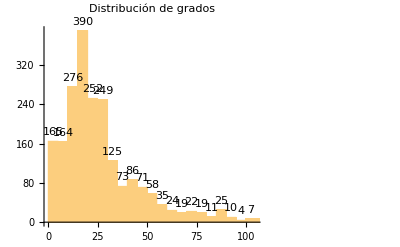

```mathematica
Histogram[VertexDegree[grafoInicialAnalisis],PlotLabel->Style["Distribución de grados","Title",14],LabelingFunction->Above]
```

```mathematica
pesoEnlaces=AnnotationValue[grafoInicialAnalisis,EdgeWeight];
```

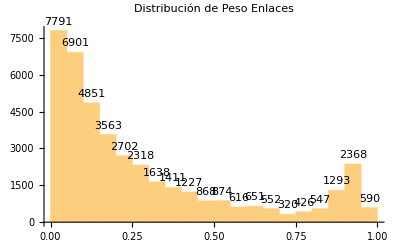

```mathematica
Histogram[pesoEnlaces,PlotLabel->Style["Distribución de Peso Enlaces","Title",14],LabelingFunction->Above]
```

Considerando los histogramas, en particular el de peso de los enlaces se va a definir una límite inferior de 0.9 para el peso de los enlaces, con el fin de filtrar conexiones que no sean tan interesantes

```mathematica
enlaces=EdgeList[grafoInicialAnalisis];
```

```mathematica
Filtrar[graph_,pesoEnlaces_,umbral_]:=Module[{enlacesSeleccionados={}},
enlaces=EdgeList[graph];
enlacesToEliminar=(#<umbral)&/@pesoEnlaces;
enlacesSeleccionados=Pick[enlaces,enlacesToEliminar];
EdgeDelete[graph,enlacesSeleccionados]
]
```

```mathematica
grafoAnalisisFiltradoPeso = Filtrar[grafoInicialAnalisis,pesoEnlaces,0.9];
```

Analisis de distribución de grados de la proyección y distribución del peso de los enlaces del grafo filtrado con un umbral del 0.9 sobre el peso de los enlaces

```mathematica
GetInfoGraph[grafoAnalisisFiltradoPeso]
```

Información del Grafo

Cantidad de Nodos = 2201

Cantidad de Enlaces = 2958

Grado promedio = 2.68787

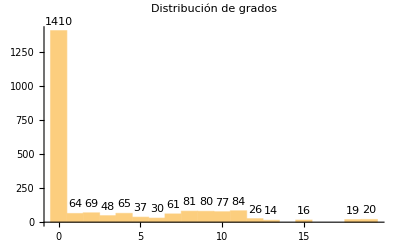

```mathematica
Histogram[VertexDegree[grafoAnalisisFiltradoPeso],PlotLabel->Style["Distribución de grados","Title",14],LabelingFunction->Above]
```

```mathematica
pesoEnlacesFiltrado=AnnotationValue[grafoAnalisisFiltradoPeso,EdgeWeight];
```

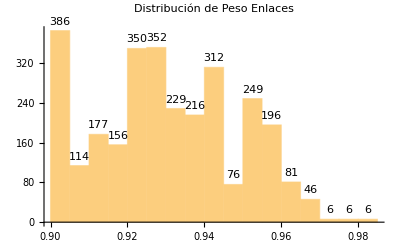

```mathematica
Histogram[pesoEnlacesFiltrado,PlotLabel->Style["Distribución de Peso Enlaces","Title",14],LabelingFunction->Above]
```

Considerando la distribución de grados y viendo que hay muchos de grado 0  se eliminan aquellos nodos de grado <=1

```mathematica
nodosDescartados=Select[VertexList[grafoAnalisisFiltradoPeso],VertexDegree[grafoAnalisisFiltradoPeso,#]<=1&];
grafoFinal=VertexDelete[grafoAnalisisFiltradoPeso,nodosDescartados];
```

```mathematica
GetInfoGraph[grafoFinal]
```

Información del Grafo

Cantidad de Nodos = 727

Cantidad de Enlaces = 2926

Grado promedio = 8.04952

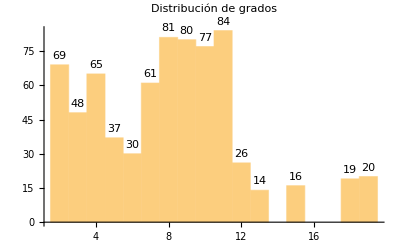

```mathematica
Histogram[VertexDegree[grafoFinal],PlotLabel->Style["Distribución de grados","Title",14],LabelingFunction->Above]
```

```mathematica
pesoEnlacesFiltradoa=AnnotationValue[grafoFinal,EdgeWeight];
```

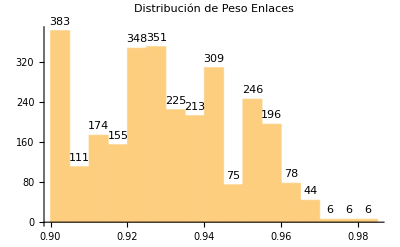

```mathematica
Histogram[pesoEnlacesFiltradoa,PlotLabel->Style["Distribución de Peso Enlaces","Title",14],LabelingFunction->Above]
```

```mathematica
GraphPlot[grafoFinal,PlotTheme->"Scientific"]
```

-Graphics-

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

GRAFO DE COMUNIDADES -  No se muestra por su dimensión de acuerdo al dataset

```mathematica
CommunityGraphPlot[grafoFinal, PlotLegends->Placed[Automatic,Below]]
```

-Graphics-

Revisión de comunidades, análisis que busca segmentar grupos de pacientes

```mathematica
comunidades=FindGraphCommunities[grafoFinal];
Length[comunidades]
```

103